# The RootSearch Package By Ted Ersek ted.ersek@navy.navy.mil

## Version History

### Version 1.0

Version 1.0 of RootSource was posted on MathSource in September of 2001.

### Version 1.1

In March of 2002 RootSearch was updated to correct minor bugs.  Unfortunately I don't recall what the bugs were.

### Version 1.2

In April 2003 RootSearch was updated to use more robust programming idioms and the current version is 1% to 2% faster than previous versions.  Also with previous versions the next cell would indicate that Sin[x] has a root at machine number 0.0 when an arbitrary precision root is expected.  With version 1.2 of RootSearch we are told Sin[x] has a root at  0.×10^-71 which is an arbitrary precision number in the interval  (-10^-70,10^-70).

```mathematica
Needs["Enhancements`RootSearch`"];
RootSearch[Sin[x]==0,{x,-2,6},PrecisionGoal->70]
```

Get::noopen: Cannot open "Enhancements`RootSearch`".

Needs::nocont: Context "Enhancements`RootSearch`" was not created when Needs was evaluated.

RootSearch[Sin[x]==0,{x,-2,6},PrecisionGoal→70]

### Version 1.3

In July 2005 version 1.3 was posted on MathSource.  

The GoldenSecant method was rewritten to make it simpler and more efficient.

Handling of arbitrary precision was greatly implroved.

Support for RootSearchSamples was added.  

Discussion was added in this notebook to explain how the RootSearch algorithm works.

An extensive list of references on the subject is provided.

### Version 1.4

In April 2006 version 1.4 was posted on MathSource.

When a package is automatically created from a notebook with all the code for this package a formatting glitch occurs. This glitch caused an incorrect setting for the RootTest option when the package is loaded using a Mac.  The package created was manually edited to correct the glitch.

Each time RootSearch is called it derives a function u[x] which has only simple roots provided the functions involved have continuous derivatives. RootSearch now derives a more efficient u[x].

## Installing and Loading the Package

To determine where to put the (RootSearch.m) file evaluate the next cell.  If this directory doesn't already have a directory called (Ersek) add one now.  The (RootSearch.m) file should then be copied to this (Ersek) directory.

```mathematica
If[$VersionNumber<5,
ToFileName[{$TopDirectory,"AddOns","ExtraPackages"}],
ToFileName[{$UserBaseDirectory,"Applications"}]
]
```

/Users/rebcabin/Library/Mathematica/Applications/

Once the (RootSearch.m) file is copied to the right directory the package can be loaded by evaluating the Needs statement in the next cell.

```mathematica
Needs["Ersek`RootSearch`"]
```

RootSearch::shdw: Symbol "RootSearch" appears in multiple contexts {"Ersek`RootSearch`", "Global`"}; definitions in context "Ersek`RootSearch`" may shadow or be shadowed by other definitions.

The next input displays the RootSearch usage message.

```mathematica
?RootSearch
```

RootSearch[lhs==rhs,{x,xmin,xmax}] tries to find all numerical solutions to the equation (lhs==rhs) with values of x between xmin and xmax.

The current version of RootSearch will only find roots of a single equation with one real variable.  The algorithm is very robust as I demonstrate with the examples that follow.  Also the algorithm is designed to give the best possible approximation to each root.  So for example, when machine precision is used you should find that the error in the location of each root is less than 1 Ulp (the distance between machine numbers).

It would be nice if RootSearch could find roots of f[z], f[x,y], and f[x,y,z] if given a region to search.  Several root finding algorithms that could be helpful here can be found in sections 9.6 and 9.7 of Numerical Recipes in C [Press, Teukolsky, Vetterling, Flannery 1994].  However, I haven't found a discussion of such algorithms that I can understand without assistance.  Please contact me if you would like to help me with this subject.

## Examples

### Example 1

In the first example RootSearch finds all 21 roots of a transcendental equation.

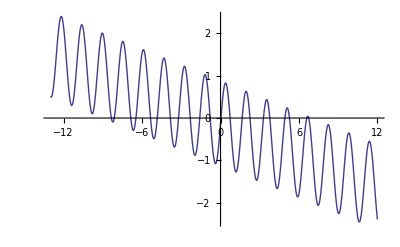

```mathematica
f1[x_]:=Sin[4 x]-(x+1)/8;
Plot[f1[x],{x,-13,12}]
```

```mathematica
soln=RootSearch[f1[x]==0,{x,-13,12}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-8.34829},{x→-8.12893},{x→-6.86295},{x→-6.47147},{x→-5.35392},{x→-4.83746},{x→-3.83638},{x→-3.21162},{x→-2.31492},{x→-1.58923},{x→-0.791902},{x→0.0323512},{x→0.730877},{x→1.65538},{x→2.25155},{x→3.28282},{x→3.76739},{x→4.92069},{x→5.27249},{x→6.59611},{x→6.73982}}

```mathematica
Length[%]
```

21

### Example 2

In the second example RootSearch finds two roots. In this case none of the traditional root finding methods such as Secant method or Newton's method will converge on the root at 1.49999,  but RootSearch has no problem. I developed a method I call GoldenSecant to ensure convergence in a case such as this.

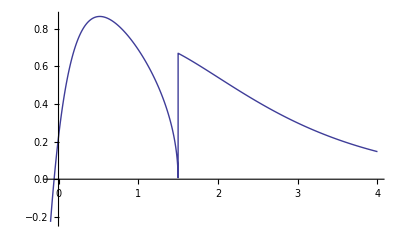

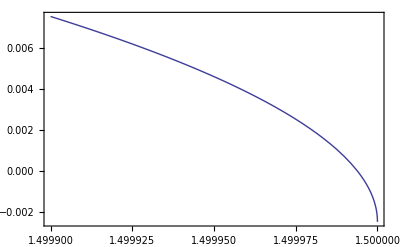

```mathematica
f2[x_]:=If[x<3/2,√(3/2-x)-Exp[-4 x],2* x Exp[-x]]
Plot[ f2[x],{x,-0.10,4},PlotPoints->500]
Plot[f2[x],{x,1.4999,1.5},PlotRange->All,Frame->True]
```

```mathematica
soln=RootSearch[f2[x]==0,{x,-25,25}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-0.0552006},{x→1.49999}}

Next we see that f2[x] evaluates to 0.0 at one root and a fairly small value at the other root.  I think you will find that no other machine number near 1.49999 will give a smaller value for Abs[f2[x]].

```mathematica
f2[x]/.soln
```

{0.,9.46855×10^-15}

### Example 3

Traditional root finding methods converge slowly at multiple roots.  RootSearch uses a little known fact that if derivatives of f[x] exist at and near a root (x=x0) then u[x] defined below has a simple root at (x=x0).  Since that is the case RootSearch will look for roots of u[x] and f[x] if f[x] can be differentiated symbolically.

```mathematica
u[x_]:=If[f[x]==0, 0, f[x]/f'[x]]
```

The next input shows that Exp[x-π]-(1-π+x) has a double root at (x=π).

```mathematica
Series[Exp[x-π]-(1-π+x),{x,π,4}]
```

1/2 (x-π)^2+1/6 (x-π)^3+1/24 (x-π)^4+O[x-π]^5

In the next example RootSearch quickly converges on the double root.

```mathematica
soln=RootSearch[Exp[x-π]==1-π+x,{x,-3,4}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→3.14159}}

The equation whose root we 'found' has a double root at (x=π). However,the next input shows that the alleged root is about 2.5×10^-8from π, but the distance between machine numbers in that region is about 4.4×10^-16.

```mathematica
π-x/.soln
```

{-2.52247×10^-8}

It turns out the RootSearch algorithm performed as advertised because (Exp[x-π]-(1-π+x)) evaluates to 0.0 at the alleged root.  In fact there are lots of machine numbers near π that solve this equation equally well. Later I demonstrate how RootSearch can get much closer to the true root of this equation.

```mathematica
(Exp[x-π]-(1-π+x)  )/.soln
```

{0.}

### Example 4

Next I give an example that demonstrates how hard RootSearch looks for roots.

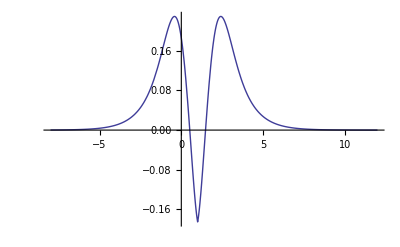

```mathematica
ClearAll[f4];
f4[x_]:=(1.5-Erf[x]-Erf[2-x])Exp[-Abs[x-1]];
Plot[f4[x],{x,-8,12},PlotRange->All]
```

In the next cell I ask FindRoot to search a range that is much larger than the range plotted above and it finds both roots.  Also notice f4[x] is very small at beginning and end of the search interval, but RootSearch doesn't claim that f4[x] has roots at either end. RootSearch will indicate that an endpoint of the search interval is a root if and only if (lhs-rhs == 0) at an endpoint.

```mathematica
soln=RootSearch[f4[x]==0,{x,-400,200}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→0.517891},{x→1.48211}}

```mathematica
f4[x]/.soln
```

{0.,6.8554×10^-17}

### Example 5

Next I give an example where RootSearch needs to look at lots of places that might contain a root.

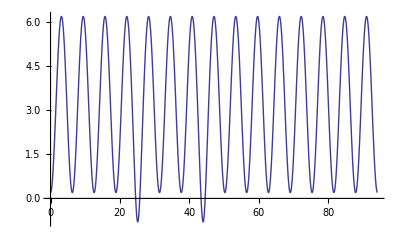

```mathematica
ClearAll[f5];
f5[x_]:=3.2-3*Cos[x]-Exp[-(x-8π)^2]-Exp[-(x-14π)^2];
Plot[f5[x],{x,0,30π}]
```

In the next cell RootSearch finds all four roots of f5[x].

```mathematica
soln=RootSearch[f5[x]==0,{x,0,30 π}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→24.5432},{x→25.7223},{x→43.3928},{x→44.5718}}

```mathematica
f5[x]/.soln
```

{0.,-3.10862×10^-15,-7.54952×10^-15,4.88498×10^-15}

### Example 6

RootSearch can find the roots of complex valued functions, and it doesn't even care if the function is undefined at some places in the interval being searched. This is demonstrated with the next example where f6[x] is complex for  (-1.2<x<1.2) and is undefined for x>1.4.

```mathematica
ClearAll[f6];
f6[x_]/;x<1.4:= √(Abs[x]-1.2) ;
RootSearch[f6[x]==0,{x,-8,8},RootTest->(#2<10^-6&)]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-1.2},{x→1.2}}

```mathematica
soln=RootSearch[f6[x]==0,{x,-8,8},PrecisionGoal->25]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision :: precset will be suppressed during this calculation.

{{x→-1.19999999999999996563832},{x→1.199999999999999893977183}}

```mathematica
f6[x]/.soln
```

{0.,0.}

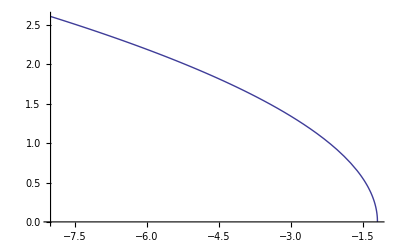

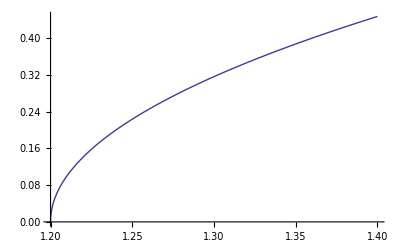

```mathematica
Plot[f6[x],{x,-8,-1.2}]
Plot[f6[x],{x,1.2,1.4}]
```

### Example 7

The Riemann Hypothesis is a famous unsolved problem that has to do with the roots of Zeta[1/2 + I y].  You can read about this problem at 
     http://mathworld.wolfram.com/RiemannHypothesis.html
The next cell makes a plot of  Abs[ Zeta[1/2 + y I] ].  You need to scroll to the right to see the whole graphic.

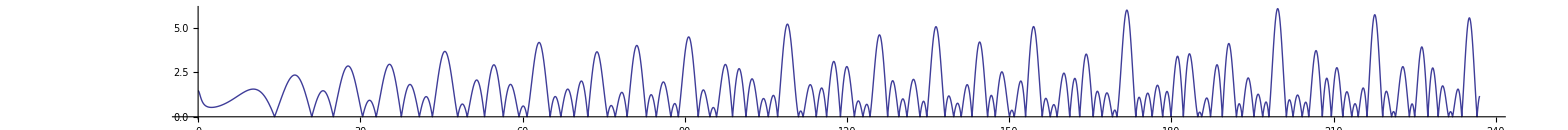

```mathematica
Plot[Abs[Zeta[1/2+y ⅈ]],{y,0,237},
ImageSize->{2000,200},AspectRatio->1/12,PlotPoints->600]
```

In the next cell RootSearch finds the first 100 roots of  Abs[Zeta[1/2 + y I]].  Notice Zeta[_] evaluates to complex numbers in this example, but RootSearch still finds the roots without problems.

```mathematica
RootSearch[Zeta[1/2+ⅈ y]==0,{y,0,237},InitialSamples->700]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{y→14.1347},{y→21.022},{y→25.0109},{y→30.4249},{y→32.9351},{y→37.5862},{y→40.9187},{y→43.3271},{y→48.0052},{y→49.7738},{y→52.9703},{y→56.4462},{y→59.347},{y→60.8318},{y→65.1125},{y→67.0798},{y→69.5464},{y→72.0672},{y→75.7047},{y→77.1448},{y→79.3374},{y→82.9104},{y→84.7355},{y→87.4253},{y→88.8091},{y→92.4919},{y→94.6513},{y→95.8706},{y→98.8312},{y→101.318},{y→103.726},{y→105.447},{y→107.169},{y→111.03},{y→111.875},{y→114.32},{y→116.227},{y→118.791},{y→121.37},{y→122.947},{y→124.257},{y→127.517},{y→129.579},{y→131.088},{y→133.498},{y→134.757},{y→138.116},{y→139.736},{y→141.124},{y→143.112},{y→146.001},{y→147.423},{y→150.054},{y→150.925},{y→153.025},{y→156.113},{y→157.598},{y→158.85},{y→161.189},{y→163.031},{y→165.537},{y→167.184},{y→169.095},{y→169.912},{y→173.412},{y→174.754},{y→176.441},{y→178.377},{y→179.916},{y→182.207},{y→184.874},{y→185.599},{y→187.229},{y→189.416},{y→192.027},{y→193.08},{y→195.265},{y→196.876},{y→198.015},{y→201.265},{y→202.494},{y→204.19},{y→205.395},{y→207.906},{y→209.577},{y→211.691},{y→213.348},{y→214.547},{y→216.17},{y→219.068},{y→220.715},{y→221.431},{y→224.007},{y→224.983},{y→227.421},{y→229.337},{y→231.25},{y→231.987},{y→233.693},{y→236.524}}

```mathematica
Length[%]
```

100

## RootSearchSamples

The usage message for RootSearchSamples is shown below.

```mathematica
?RootSearchSamples
```

RootSearchSamples returns a list of points where the equation given to RootSearch was sampled during the last use of RootSearch. If RootSearch[lhs==rhs,{x,xmin,xmax}] was evaluated. Then RootSearchSamples returns {{x1,y1},{x2,y2}, ...} where yn is the value of (lhs-rhs) at x=xn. 
Points where (lhs-rhs) did not evaluate to a numeric value are not included in the list returned.

RootSearchSamples is useful for monitoring how well RootSearch converges on roots. An example is given below where only 19 samples are needed to find two roots.

```mathematica
ClearAll[f4];
f4[x_]:=(1.5-Erf[x]-Erf[2-x])Exp[-Abs[x-1]];
RootSearch[f4[x]==0,{x,-2,5},InitialSamples->4]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→0.517891},{x→1.48211}}

```mathematica
RootSearchSamples//TableForm
```

-2. | 0.0744477
0. | 0.185661
0.376991 | 0.0620264
0.516478 | 0.000643118
0.517884 | 3.2925×10^-6
0.517891 | 2.05662×10^-16
0.517891 | 0.
0.517891 | -1.73841×10^-10
0.566124 | -0.0220761
0.753254 | -0.10577
1.26121 | -0.0996567
1.48192 | -0.0000883347
1.48211 | -6.8554×10^-17
1.48211 | 6.8554×10^-17
1.48211 | 1.88194×10^-12
1.48211 | 6.84424×10^-8
1.48743 | 0.00241908
1.6902 | 0.0893282
2.62714 | 0.221067
5. | 0.0274731

```mathematica
RootSearchSamples//Length
```

20

It also allows you use you own judgement to see if there may be additional roots that were not returned.

```mathematica
ClearAll[f5];
f5[x_]:=3.2-3*Cos[x]-Exp[-(x-8π)^2]-Exp[-(x-14π)^2];
RootSearch[f5[x]==0,{x,0,30 π}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→24.5432},{x→25.7223},{x→43.3928},{x→44.5718}}

If you want to see if RootSearch missed some roots, you don't need to use Plot when all the samples RootSearch took are available for you to work with.  The next cell plots the samples taken by RootSearch.

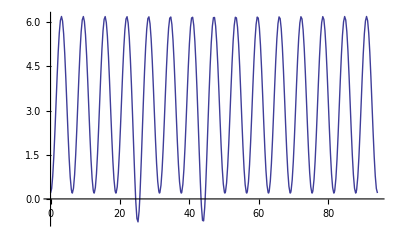

```mathematica
plt=ListLinePlot[RootSearchSamples]
```

Then you can use the next cell to get all the samples near the roots.

```mathematica
Cases[RootSearchSamples,{_,_?(Abs[#]<0.1&)}]//TableForm
```

24.5381 | 0.0127759
24.543 | 0.000382321
24.5432 | 6.58258×10^-8
24.5432 | 3.37508×10^-13
24.5432 | 0.
25.7223 | -3.10862×10^-15
25.7223 | 3.56253×10^-11
25.7223 | 1.22797×10^-6
25.7225 | 0.000668854
25.7388 | 0.0416147
43.3822 | 0.0265048
43.392 | 0.00181632
43.3928 | 1.298×10^-6
43.3928 | 6.32698×10^-11
43.3928 | 1.06581×10^-14
43.3928 | -7.54952×10^-15
44.5718 | 4.88498×10^-15
44.5718 | 4.25961×10^-10
44.5718 | 3.87675×10^-6
44.5731 | 0.00327675
44.5857 | 0.0349921

The next cell shows all the samples taken near one of the local minimum of  f5[x].

```mathematica
Cases[RootSearchSamples,{_?(5<#<9&),_}]//TableForm
```

5.04922 | 2.2085
5.3538 | 1.40502
5.67116 | 0.744549
5.99086 | 0.327272
6.01874 | 0.304288
6.15969 | 0.222847
6.23017 | 0.204215
6.26541 | 0.200474
6.30064 | 0.200457
6.61483 | 0.363479
6.93685 | 0.818419
7.25075 | 1.49807
7.56159 | 2.33527
7.87608 | 3.26629
8.19673 | 4.20822
8.51673 | 5.04587
8.82266 | 5.67242

## RootSearch Options

The next input returns the RootSearch options, which are each explained below.

```mathematica
Options[RootSearch]//TableForm
```

InitialSamples→300
RootTest:>(Abs[#2]≤10^5 (Abs[#1]+$MinMachineNumber) $MachineEpsilon&)
MaxBrentSteps→150
MaxSecantSteps→150
PrecisionGoal:>$MachinePrecision
InitialPrecision:>$MachinePrecision

### PrecisionGoal

The next input displays the PrecisionGoal usage message.

```mathematica
?PrecisionGoal
```

PrecisionGoal is an option for various numerical operations which specifies how many effective digits of precision should be sought in the final result.

In the next cell I use PrecisionGoal to approximate roots with high precision.

```mathematica
soln=RootSearch[Sin[x]==(x+1)/8,{x,-10,10},PrecisionGoal->35]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision :: precset will be suppressed during this calculation.

{{x→-8.28114773688421085895293214234475},{x→-7.1625203762270904400685296537390978},{x→-2.9015958868328709147284087746566058},{x→0.14341846117333293841750225818695085},{x→2.6656206948450314724160832041644766}}

I think you will find that no other values with 35 digits of precision give a better estimate of the roots.

```mathematica
Sin[x]-(x+1)/8/.soln
```

{0.,0.,0.,0.,0.}

When trying to find roots with high precision, you generally need to express the equation without using machine precision numbers.
In the next cell the previous example is repeated with use of machine precision numbers in the equation and we don't get the roots with higher precision.

```mathematica
soln=RootSearch[Sin[x]==x/8+0.125,{x,-10,10},PrecisionGoal->35]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision :: precset will be suppressed during this calculation.

{{x→-8.28115},{x→-7.16252},{x→-2.9016},{x→0.143418},{x→2.66562}}

```mathematica
Sin[x]-(x+1)/8/.soln
```

{2.22045×10^-16,1.11022×10^-16,1.66533×10^-16,0.,5.55112×10^-17}

In the next cell, we find some roots of the Riemann Zeta function with high precision.

```mathematica
soln=RootSearch[Zeta[1/2+ⅈ y]==0,{y,0,40},PrecisionGoal->30]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision :: precset will be suppressed during this calculation.

{{y→14.1347251417346937904572519836},{y→21.0220396387715549926284795939},{y→25.0108575801456887632137909926},{y→30.4248761258595132103118975306},{y→32.9350615877391896906623689641},{y→37.5861781588256712572177634807}}

```mathematica
Zeta[1/2+ⅈ y]/.soln
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

### InitialPrecision

The next input displays the InitialPrecision usage message.

```mathematica
?InitialPrecision
```

InitialPrecision is an option for RootSearch which specifies the precision of the values where a function is intially sampled. If the InitialPrecision setting is a positive value less than or equal to $MachinePrecision, then machine numbers are used. If the setting is larger than $MachinePrecision the setting specifies the level of arbitrary precision used.

An earlier example found a double root to the equation (Exp[x-π]==1-π+x).  RootSearch can converge very close to the exact root of this equation, if it avoids sampling at machine precision numbers.  In the next input the setting  (InitialPrecision→18) is used instead of the default setting  (InitialPrecision:>$MachinePrecision). 

Note:  The root found in this example is a machine precision number. This is due to use of the default setting (PrecisionGoal:>$MachinePrecision) in which case RootSearch applies N[roots] just before the roots are returned.

```mathematica
soln=RootSearch[Exp[x-π]==1-π+x,{x,-3,4},InitialPrecision->18]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision :: precset will be suppressed during this calculation.

{{x→3.14159}}

The next input shows that the approximate value of the double root is very close to the exact machine number used for π.

```mathematica
x-π/.soln
```

{0.}

In some pathological cases we have to avoid use of machine precision numbers to get reliable results. The next cell gives one such example.

```mathematica
expr=Sin[1.1+x]-Sin[1.71* x];
big=10^12;
soln=RootSearch[expr==0,{x,big,big+20}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12},{x→1.×10^12}}

```mathematica
expr/.soln
```

{-0.0000223968,0.000148376,0.0000922274,-6.21163×10^-7,0.0000162468,0.0000580443,0.000159126,-0.0000436552,-2.97964×10^-6,-9.46214×10^-6,-0.000104878}

In the previous cell we see that the roots found don't solve the equation very well.  To get better results we must first modify our expression as in the next cell  to make sure it's free of machine precision numbers.  In some cases infinite precision is very time consuming and it would be better to use something like (num_Real:>SetPrecision[num,70]).

```mathematica
expr=expr/.num_Real:>SetPrecision[num,∞]
```

-Sin[(1925288840700887 x)/1125899906842624]+Sin[2476979795053773/2251799813685248+x]

In the next two cells we see that using values for (x) with 18 digits of precision gives a value for (expr) with less than 5 digits of precision. It seems we are better off using values for (x) with 28 digits of precision.

```mathematica
expr/.x->N[big+10,18]//InputForm
```

-0.09071979895609731242056071284170119597`4.743779769119613

```mathematica
expr/.x->N[big+10,28]//InputForm
```

-0.09071979895609731242056071284170119589`14.743779769119614

In the next cell RootSearch does all the work with arbitrary precision and gives a good approximation of the roots.  In some cases you can get good results with a setting for InitialPrecision that is a few digits less than the setting of PrecisionGoal. But for best reliability I recommend you always use (InitialPrecision→InitP, PrecisionGoal→GoalP) with (InitP≤GoalP).

```mathematica
soln=RootSearch[expr==0,{x,big,big+20},InitialPrecision->28,PrecisionGoal->28]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision :: precset will be suppressed during this calculation.

{{x→1.00000000000066906715117705×10^12},{x→1.000000000002987585714711953×10^12},{x→1.000000000005306104278246855×10^12},{x→1.000000000007624622841781758×10^12},{x→1.000000000008224669176064825×10^12},{x→1.000000000009943141405316661×10^12},{x→1.000000000012261659968851564×10^12},{x→1.000000000014580178532386466×10^12},{x→1.000000000016898697095921369×10^12},{x→1.000000000017074225946740299×10^12},{x→1.000000000019217215659456272×10^12}}

```mathematica
expr/.soln
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### RootTest

Often times we can find a value where a function is 'very close' to zero and we say it is a root if we can't find a near by value where the function is closer to zero.  However, it could be that the function isn't zero at any point near the alleged root. How does one decide if a suspected root actually is a root? The RootTest option allows a user to control what is considered a root, and causes RootSearch to only return potential roots that meet the specified condition. The next input displays the RootTest usage message.

```mathematica
?RootTest
```

RootTest is an option for RootSearch which determines whether specific values are roots of an equation. Once the core algorithm for RootSearch[lhs==rhs,{x,xmin,xmax}] is finished a list of points {{x1,y1},{x2,y2}, ...} is effectively made where each xi is a likely root and yi is the value of (lhs-rhs) when (x=xi). Only the likely roots for which RootTest is True are returned.  The RootTest setting should be a function of one or two arguments where xi is the first argument and yi is the second argument.

The function f7[x] defined in the next cell can demonstrate the utility of the RootTest option.  In this case f7[x] changes sign at (x= π/2) and (x= -π/2) and the plot is not continuous at those points. In fact the equation (f7[x]==0) has no real roots.

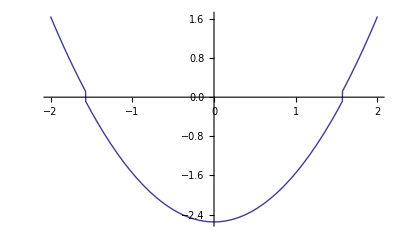

```mathematica
ClearAll[f7];
f7[x_]:=If[Abs[x]<π/2,x^2-2.55,x^2-2.35];
Plot[f7[x],{x,-2,2}]
```

In the next input RootSearch says f7[x] has a roots at (x= -1.5708) and (x=1.5708).  The RootTest setting in this example keeps any potential root where f7[x] is less than 0.1.

```mathematica
RootSearch[f7[x]==0,{x,-3,3},RootTest->(Abs[#2]<0.1&)]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-1.5708},{x→1.5708}}

In the next input RootSearch tells us no roots were found. In this case the RootSearch algorithm converged on the same values as the previous example, but the roots were discarded because of the RootTest setting. With the setting in this example only potential roots for which (Abs[f7[x]]<0.0001) are returned.

```mathematica
RootSearch[f7[x]==0,{x,-3,3},RootTest->(Abs[#2]<0.0001&)]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{}

The RootSearch setting in the next input causes any potential root to be accepted. Notice in this case the RootTest setting isn't simply True, it's a function that always returns True.  This setting is useful if you think the derivative of (lhs-rhs) is very steep at some of the roots you are looking for.

```mathematica
RootSearch[f7[x]==0,{x,-3,3},RootTest->(True&)]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-1.5708},{x→1.5708}}

By using the setting RootTest→(True&) you are assured that every potential root that RootSearch converged on is returned.  However, you must keep in mind that some of the roots returned may not be roots at all. For example in the next cell RootSearch tells us ArcCot[x-1/3] has a root at (x→0.333333) which is clearly not a root.

```mathematica
RootSearch[ArcCot[x-1/3]==0,{x,0,3},RootTest->(True&)]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→0.333333}}

#### The default setting for -- RootTest

The next input displays the default RootTest setting.

```mathematica
Options[RootSearch,RootTest]
```

{RootTest:>(Abs[#2]≤10^5 (Abs[#1]+$MinMachineNumber) $MachineEpsilon&)}

When the default setting (PrecisionGoal:>$MachinePrecision) is used RootSearch returns each root with an error of less than 1 Ulp (the distance between adjacent machine numbers).  1 Ulp at a machine number (x) satisfies the following inequality.

```mathematica
Ulp[x]≤(Abs[x]+$MinMachineNumber)$MachineEpsilon
```

So if (Abs[f' [x]]<10^5) at a root, then the value of f[x] at the approximate root will satisfy the following inequality which is used in the default RootTest setting.

```mathematica
Abs[f[x]]≤10^5(Abs[x]+$MinMachineNumber)$MachineEpsilon
```

The default RootTest is an implementation of this inequality, and it normally gives good results.

### MaxBrentSteps

The next input displays the MaxBrentSteps usage message.

```mathematica
?MaxBrentSteps
```

MaxBrentSteps is an option for RootSearch which specifies the maximum number of steps the algorithm should take when attempting to find a specific root using Brent's method.

Notice Brent's method is sometimes used by the Mathematica FindRoot function and by the RootSearch function.  The default setting (MaxBrentSteps→150) is a little more than sufficient for even the most difficult problems I tried.  RootSearch should be very robust with this default setting.  In the next cell I use the setting (MaxBrentSteps→100) and RootSearch doesn't find the multiple roots in the given interval.  Since Abs'[x] is not defined RootSearch can not use a trick discussed above to ensure rapid convergence at the multiple roots.

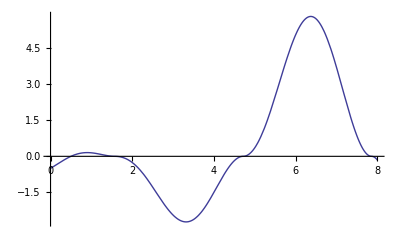

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→0.5}}

```mathematica
Plot[(x-1/2) Cos[x]Abs[Cos[x]],{x,0,8}]

RootSearch[(x-1/2) Cos[x]Abs[Cos[x]]==0,{x,0,8},MaxBrentSteps->100]
```

The next cell finds all the roots.

```mathematica
RootSearch[(x-1/2) Cos[x]Abs[Cos[x]]==0,{x,0,8},MaxBrentSteps->150]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→0.5},{x→1.5708},{x→4.71239},{x→7.85398}}

### MaxSecantSteps

The next input displays the MaxSecantSteps usage message.

```mathematica
?MaxSecantSteps
```

MaxSecantSteps is an option for RootSearch which specifies the maximum number of steps the algorithm should take when attempting to find a specific root using a modified secant method.

The default setting (MaxSecantSteps→90) is a little more than sufficient for even the most difficult problems I tried. RootSearch should work very well with this default setting. In the next input I use the setting (MaxSecantSteps→8) and RootSearch doesn't find the root at 1.49999.

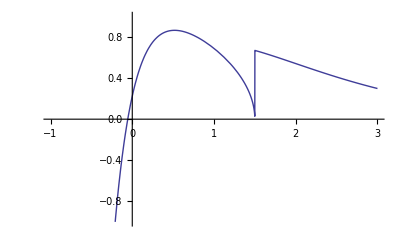

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-0.0552006}}

```mathematica
ClearAll[f2];
f2[x_]:=If[x<3/2,√(3/2-x)-Exp[-4 x],2* x Exp[-x]]
Plot[f2[x],{x,-1,3},PlotRange->{-1,1}]

soln=RootSearch[f2[x]==0,{x,-25,25},MaxSecantSteps->8]
```

In the next cell RootSearch finds both roots.

```mathematica
soln=RootSearch[f2[x]==0,{x,-25,25},MaxSecantSteps->90]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-0.0552006},{x→1.49999}}

### InitialSamples

The next input displays the InitialSamples usage message.

```mathematica
?InitialSamples
```

InitialSamples is an option for RootSearch which specifies the number of nearly equally spaced samples that should be taken before root finding methods are used to converge on roots.

The setting (InitialSamples→300) is used by default, and this allows a reasonable assurance that all roots have been found without spending a long time sampling the function.  The next input demonstrates what can happen if a small setting for this option is used. In this example RootSearch finds 5 roots when there are actually 21 roots.

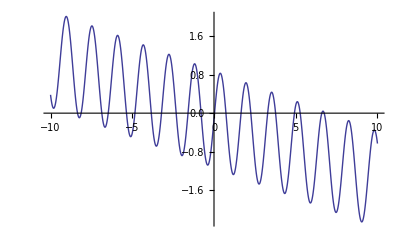

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-8.34829},{x→-8.12893},{x→-5.35392},{x→-3.83638},{x→-3.21162},{x→-0.791902},{x→0.0323512},{x→0.730877},{x→3.28282},{x→3.76739},{x→5.27249}}

```mathematica
Plot[Sin[4 x]-(x+1)/8,{x,-10,10}]

soln=RootSearch[Sin[4 x]==(x+1)/8,{x,-10,10},InitialSamples->22]
```

In the next cell RootSearch finds all 21 roots with 300 initial samples.

```mathematica
soln=RootSearch[Sin[4 x]==(x+1)/8,{x,-10,10},InitialSamples->300]
Length[soln]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→-8.34829},{x→-8.12893},{x→-6.86295},{x→-6.47147},{x→-5.35392},{x→-4.83746},{x→-3.83638},{x→-3.21162},{x→-2.31492},{x→-1.58923},{x→-0.791902},{x→0.0323512},{x→0.730877},{x→1.65538},{x→2.25155},{x→3.28282},{x→3.76739},{x→4.92069},{x→5.27249},{x→6.59611},{x→6.73982}}

21

## The RootSearch Algorithm

When given  RootSearch[lhs==rhs, {x,xmin,xmax}]  the algorithm starts by determining if  D[lhs-rhs, x] can be computed.  When the derivative can be computed a routine called SearchForRootsU is used.  Otherwise the routine SearchForRootsF is used.

The first thing that happens in SearchForRootsU and SearchForRootsF is that they make a list of points where 
f[x_] :=(lhs-rhs) is sampled.  Next SearchForRootsU or  SearchForRootsF determines that there may be roots between certain samples and appropriate algorithms are used to narrow the approximation of each potential root. 

Once SearchForRootsU or SearchForRootsF is finished the list of potential roots is screened and only those that pass the test specified by the setting of the RootTest option are returned.  Details are discussed in the sections that follow.  

Brent's root finding algorithm is often used by RootSearch.  Details of Brent's method can be found in section 9.3 of Numerical Recipes in C [Press, Teukolsky, Vetterling, Flannery 1994].  Brent's method was originally published in [Brent 1971].  Brent's method is very robust and efficient and theorems supporting this can be found in [Brent 1973].

I developed the GoldenSecant method for use in RootSearch but never had anything about it published. I am puzzled about why an algorithm similar to GoldenSecant has never been published.  My GoldenSecant method uses the well known secant method which is presented in section 9.2 of Numerical Recipes in C [Press, Teukolsky, Vetterling, Flannery 1994].  My GoldenSecant method also uses estimates based on the Golden-Section find minimum algorithm which is presented in section 10.1 of Numerical Recipes in C [Press, Teukolsky, Vetterling, Flannery 1994].

### Determine if Mathematica can compute the derivative of (lhs-rhs)

When given RootSearch[ lhs==rhs, { x, xmin, xmax}] we are searching for roots of  f[x]=(lhs-rhs).  Popular root finding methods such as Newton's method, secant method, and Brent's method converge slowly on a multiple root of f[x].  However, we have a very effective trick for efficiently converging on multiple roots.  If derivatives of f[x] exist at and near a root (x=x0) of f[x]. Then (x=x0) is a first order root of   u[x_]:=If[f[x]==0,0,f'[x]/f[x]].  Notice this trick doesn't require that we know the order of the root, or even if the root is a multiple root.  Since this trick is so effective we will look for roots of u[x] instead of roots of f[x], but this requires that Mathematica knows how to compute D[f[x], x].  
Sometimes (lhs-rhs) involves functions such as Abs[x] which Mathematica can't compute the derivative of, the RootSearch algorithm automatically detects this condition and in that case it finds roots of f[x].

When Mathematica can compute D[f[x], x]  RootSearch uses a function in the package called SearchForRootsU which finds roots of u[x] defined above.  When Mathematica can't compute D[f[x], x] RootSearch uses a function in the package called SearchForRootsF which finds roots of f[x]. 

I discovered on my own that if f[x] is well behaved any roots of u[x] above are simple roots.  After making my discovery I found  http://mathworld.wolfram.com/SchroedersMethod.html  which references [Stewart 1993] and in that paper Ernst Schröder is credited with publishing this property of u[x] in 1870.

### Make a list of initial Samples

The first thing done by SearchForRootsU and SearchForRootsF is that they make a list of points between xmin, and xmax where f[x] is sampled.   The end points (xmin and xmax) are included in the list of sample points.  The number of points in the list is determined by the option InitialSamples, and the samples are nearly equally spaced with a bit of noise added.  The noise is added to reduce the chance that details are missed if f[x] is periodic.  If  ( xmin < 0 < xmax ) the value 0 is added to the list without noise, and no noise is added to the points at xmin, and xmax.  Depending on the settings of the options InitialPrecision and PrecisionGoal the list of points may be converted to arbitrary precision numbers.  Once a list of points is made f[x] is sampled at each point in the list.  It may turn out that f[x] evaluates to a complex number, and in that case the complex number is converted to a real number that normally allows efficient convergence to a root.  For details on this conversion see the definition of MakeReal in the package and the associated comments in the code. 
Evaluating u[x] is more time consuming than evaluation f[x], so only f[x] is evaluated at each initial sample.

### SearchForRootsU

SearchForRootsU collects potentially five sets of roots as described below and returns  Flatten[{soln1, soln2, soln3, soln4, soln5}].  This scheme only requires computing u[x] where u[x] changes sign.

soln1 = ( Points where the initial samples turn out to be roots of f[x]. )
soln2 = ( Roots found using Brent's method on u[x] where f[x] and u[x] both change sign. )
soln3 = ( Roots found using Brent's method on f[x] where f[x] changes sign but u[x] doesn't change sign. )
soln4 = ( Roots found using Brent's method on u[x] where there are consecutive initial samples x1, x2, x3 meeting conditions 1, 2, 3 below and either condition (4.a) or (4.b) is also true.)
soln5 = ( Roots found using the GoldenSecant method on f[x] where there are consecutive initial samples x1, x2, x3 meeting conditions 1, 2, 3 below and neither conditions (4.a) or (4.b) are true. ) 

The sections that follow discuss finding solutions (soln2, soln3, soln4, soln5) in greater detail.  

Conditions used for soln4 and soln5:
(1)   x1<x2<x3 
(2)   f[x1]], f[x2], f[x3] are (all positive) or (all negative).
(3)   ( Abs[f[x2]] < Abs[f[x1]] )  and  ( Abs[f[x2]] < Abs[f[x3]] ).
(4.a)   u[x] is positive or negative at x1 and u[x] has opposite sign at x2 and x3.
(4.b)   u[x] is positive or negative at x3 and u[x] has opposite sign at x1 and x2.

#### Soln2

Below we have an example where f[x] has a third order root at (x=π).  Once f[x] is sampled at 
(x1 = 3.05) and (x2 = 3.2) we could use Brent's method on f[x] to converge on the root.  However, from the plots made below it's easy to see that converging on a root of u[x] is much easier. In this case Brent's method is used to converge on the root of u[x]  at (x=π).

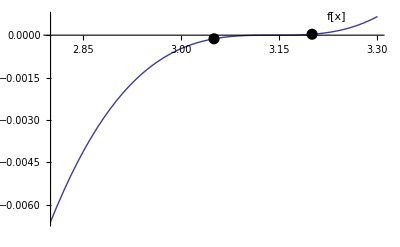

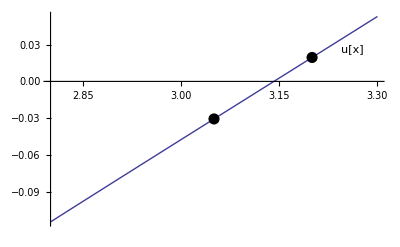

```mathematica
f[x_]:=Sin[x]+x-π;
u[x_?NumericQ]:=If[f[x]==0,f[x],f[x]/f'[x]];

{x1,x2}={3.05,3.2};
{f1,f2,u1,u2}={f[x1],f[x2],u[x1],u[x2]};

Plot[f[x],{x,2.8,3.3},Epilog->{PointSize[0.02], Point[{x1,f1}],Point[{x2,f2}],
Text["f[x]",Offset[{24,18},{x2,f2}]]}]

Plot[u[x],{x,2.8,3.3},Epilog->{PointSize[0.02], Point[{x1,u1}],Point[{x2,u2}],
Text["u[x]",Offset[{40,32},{x2,f2}]]}]
```

#### Soln3

It's possible that samples are found where f[x] changes sign, but u[x] doesn't change sign.  The next cell makes a graphic where that is the case.  When that happens we use Brent's method to converge on a root of f[x].  In this case Brent's method can't converge quickly on a multiple root, but at least it's guaranteed to converge if given enough iterations.  When Brent's method is used to converge on a first order root, it normally converges very quickly.

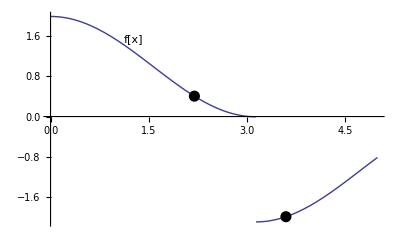

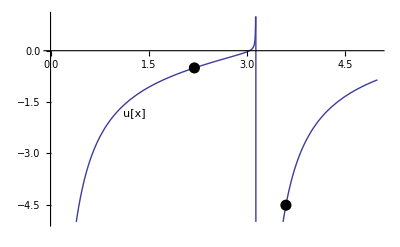

```mathematica
f[x_]:=(Cos[x]+0.995)(1-UnitStep[x-π])+(Cos[x]-1.1)(1-UnitStep[π-x]);
u[x_?NumericQ]:=If[f[x]==0,f[x],f[x]/f'[x]];

{x0,x1}={2.2,3.6};
{f0,f1,u0,u1}={f[x0],f[x1],u[x0],u[x1]};

Plot[f[x],{x,0,5},Epilog->{PointSize[0.02], Point[{x0,f0}],Point[{x1,f1}],
Text["f[x]",Offset[{18,0},{1.0,f[1.0]}]]}]

Plot[u[x],{x,0,5},PlotRange->{-5,1},Epilog->{PointSize[0.02], Point[{x0,u0}],Point[{x1,u1}],
Text["u[x]",Offset[{18,0},{1.0,u[1.0]}]]}]
```

#### Soln4

In other cases samples are found where f[x] doesn't change sign, but  f[x]  has a local extremum and u[x] changes sign at the local extremum.  An example illustrating that case is shown with the graphic made below.  In this case Brent's method is used to converge on a root of u[x].

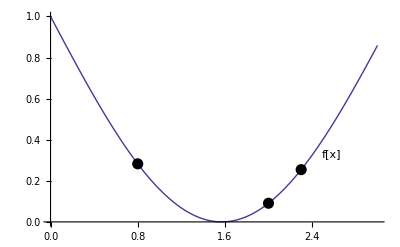

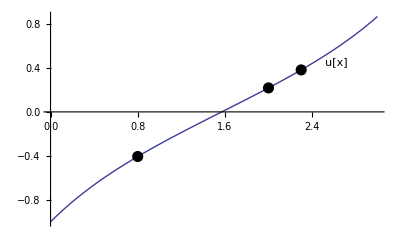

```mathematica
f[x_]:=1-Sin[x];
u[x_?NumericQ]:=If[f[x]==0,f[x],f[x]/f'[x]];

{x1,x2,x3}={0.8,2.0,2.3};
{f1,f2,f3,u1,u2,u3}={f[x1],f[x2],f[x3],u[x1],u[x2],u[x3]};

Plot[f[x],{x,0,3},Epilog->{PointSize[0.02], Point[{x1,f1}],Point[{x2,f2}],Point[{x3,f3}],
Text["f[x]",Offset[{30,16},{x3,f3}]]}]

Plot[u[x],{x,0,3},Epilog->{PointSize[0.02], Point[{x1,u1}],Point[{x2,u2}],Point[{x3,u3}],
Text["u[x]",Offset[{35,8},{x3,u3}]]}]
```

#### Soln5

It's also possible that samples are found where f[x] has a local extremum and neither f[x] or u[x] change sign.  In that case Brent's method can't be used on either f[x] or u[x].  What we need here is a method of converging on the local extrema of f[x], and we want to efficiently converge in the event the local extrema is at a root of f[x].  

In this case RootSearch uses an algorithm I call GoldenSecant.  The idea is that a secant step is used on most iterations, but a GoldenSection find minimum step is taken when a secant step would be poor choice. 

The next cell makes a graphic for a situation where my GoldenSecant method is useful.

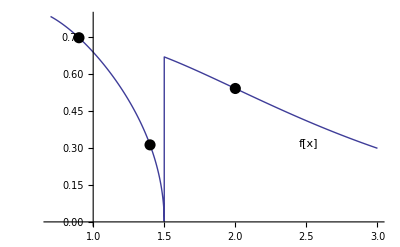

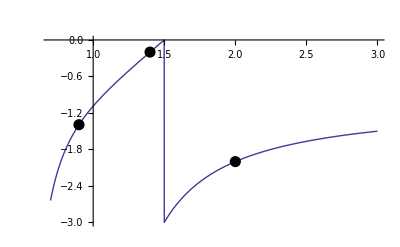

```mathematica
f[x_]:=If[x<3/2,√(3/2-x)-Exp[-4 x],2* x Exp[-x]];
u[x_?NumericQ]:=If[f[x]==0,f[x],f[x]/f'[x]];

{xa,xb,xc}={0.9,1.4,2.0};
{fa,fb,fc,ua,ub,uc}={f[xa],f[xb],f[xc],u[xa],u[xb],u[xc]};
Plot[ f[x],{x,0.7,3},Epilog->{PointSize[0.02], Point[{xa,fa}],Point[{xb,fb}],Point[{xc,fc}],
Text["f[x]",Offset[{30,16},{x3,f3}]]},
PlotPoints->700
]
Plot[u[x],{x,0.7,3},
Epilog->{PointSize[0.02], Point[{xa,ua}],Point[{xb,ub}],Point[{xc,uc}],
Text["f[x]",Offset[{30,16},{x3,f3}]]}]
```

### SearchForRootsF

SearchForRootsF collects potentially three sets of roots as described below and returns  Flatten[{soln1, soln2, soln3}].

soln1 = ( Points where the initial samples turn out to be roots of f[x]. )
soln2 = ( Roots found using Brent's method on f[x] where f[x] changes sign. )
soln3 = ( Roots found using GoldenSecant method on f[x] where Abs[f[x]] has a local minimum, and f[x] does not change sign.)

Finding the three sets of solutions above is similar to finding the solutions using SearchForRootsU above.

### The roots found are screened

SearchForRootsU or SearchForRootsF returns a list of roots found.  Only roots that pass the test specified by the RootTest option are returned by RootSearch.

### Changes to Brent's method

#### Tighter convergence check for Brent's method

As written by Van Wijngaarden, Dekker, and Brent the method stops when the root is trapped to 
an interval (a < x < b) with (b-a) ≤ (2*$MachineEpsilon+$MinMachineNumber).  I was never able to find an explanation for why $MachineEpsilon is multiplied by two.  It looks to me like this is done to account for the fact that the distance between machine numbers has sudden jumps at some places.  For example on my computer 
{(8-8.882×10^-16),  8.0, (8+1.776×10^-15)} are three consecutive machine numbers.  The distance between machine numbers always increases by a factor of 2 and only happens at powers of 2.  There is one exception for machine numbers adjacent to 0.0.

In my implementation I account for this using my function Ulp2 that ensures each new estimated root is not a number that was previously considered as a potential root.  As a result my implementation of Brent's method either finds a number where f[x] is exactly 0.0 or returns one of two adjacent approximate numbers where f[x] changes sign.

#### Brent's method is modified to see if it's converging on a pole

Suppose we are trying to find a root of Tan[x] starting with samples at (x=1.5) and (x=2.0).  Brent's method can be used here because Tan[x] has opposite sign at the two values.  However, Brent's method will slowly converge on the pole at (x = π/2). My implementation of Brent's method uses a function called PoleTest to see if Brent's method is likely converging on a pole and quits early when this is the case.  For more details see the comments near the implementation of PoleTest in the code.

### The GoldenSecant method

The GoldenSecant method keeps track of three points {x1,f1}, {x2,f2}, and {x3,f3} which are used to 
select a value newX which is the next estimate of the root.  If a sample is found where f[x] changes sign Brent's method is used to further refine the estimate of the root.  On each iteration newX replaces either  x1 or  x3 and the points are shuffled to ensure the following are true. 
   •   (x1<x2<x3)  or  (x3<x2<x1) 
   •   Abs[ x2-x1 ] ≤ Abs[ x2-x3 ]
   •   (f2/f1≤1) and (f2/f3≤1)
On each iteration a secant step using points {x1,f1} and {x2,f2} is considered.  If the secant step considered is larger than Abs[x3-x2] a Golden-Section find minimum step is used instead.  Also if the direction of a secant step is in the opposite direction than the previous step then a Golden-Section find minimum step is used if the secant step would have been larger. This gives a new estimate called newX and we always ensure (newX - x2 ≠ 0) and (newX - x3 ≠ 0).  In the event the algorithm is converging on a local exremum the secant steps are consistently much larger than Abs[x3-x2] and the algorithm will quit before reaching the maximum number of iterations.  Often times the algorithm determines that a root has been found once it narrows the root to the smallest possible interval for the precision being used.

It's well known that the secant method converges fairly efficiently, but often fails to converge. By overriding the secant estimate with a Golden-Section find minimum step in some cases we can guarantee that the method converges on either a local exremum or a root.

#### An example when a secant step is used

The next two cells show an example where a secant step using points  p1={x1, f1} and  p2={x2, f2} gives 
newX= 2.52157 as a new estimate of the root.  This is a case where the secant step gives a better approximation of the root.  In a case such as this the Golden-Secant method uses the secant estimate because the new estimate is inside Interval[{x2, x3}].

```mathematica
f[x_]:=Cos[x]+0.95

{x1,x2,x3}={1.5,1.64,5.0};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

2.52157

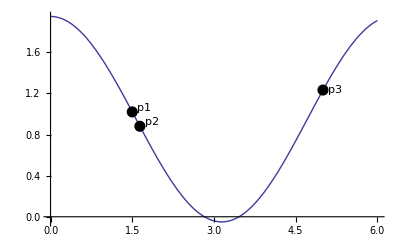

```mathematica
{f1,f2,f3}={f[x1],f[x2],f[x3]};

Plot[f[x],{x,0,6},Epilog->{PointSize[0.02], Point[{x1,f1}],Point[{x2,f2}],Point[{x3,f3}],
Text["p1",Offset[{12,4},{x1,f1}]],
Text["p2",Offset[{12,4},{x2,f2}]],
Text["p3",Offset[{12,0},{x3,f3}]]
}]
```

#### An example when a secant step leads us astray

Suppose we are trying to find the roots between 1.495 and 4.8 of  (Abs[Sin[x]]-x/10+0.313).  Further suppose we started with the initial samples that the next cell displays. Based on these initial samples we would be wise to look harder for a root near samples {3.095, 0.0500758}, {3.195, 0.046882}, and {3.295, 0.136306}.

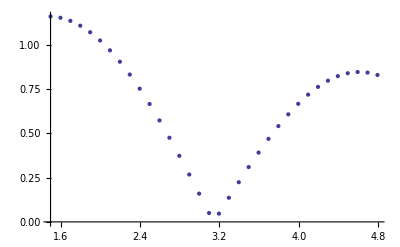

{{3.095,0.0500758},{3.195,0.046882},{3.295,0.136306}}

```mathematica
xpnts=Range[1.495,4.8,0.1];
f[x_]:=Abs[Sin[x]]-x/10+0.313;
data=Transpose[{xpnts,f/@xpnts}];
ListPlot[data]
{{x1,f1},{x2,f2},{x3,f3}}=Take[data,{17,19}]
```

In the next cell we see that a secant step using points {x1, f1}={3.095, 0.0500758} and {x2, f2}={3.195, 0.046882} gives a new approximate root of 4.66289 which is well outside the interval that we suspect contains a root.  In fact we already have initial samples near 4.66289 and found little reason to suspect there is a root there.  In a case such as this the GoldenSecant method decides the secant step was a poor approximation of the root and takes a Golden-Section find minimum step instead.  So the new estimate of the root is approximately  ( newX = x2+0.381966*(x3-x2) ).

```mathematica
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

4.66289

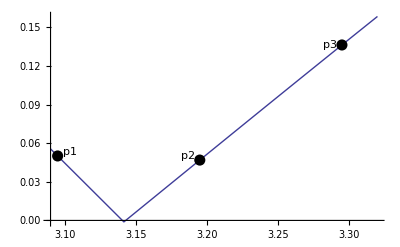

```mathematica
{f1,f2,f3}={f[x1],f[x2],f[x3]};

Plot[f[x],{x,3.09,3.32},
AxesOrigin->{3.09,0},Epilog->{PointSize[0.02], Point[{x1,f1}],Point[{x2,f2}],Point[{x3,f3}],
Text["p1",Offset[{12,4},{x1,f1}]],
Text["p2",Offset[{-12,4},{x2,f2}]],
Text["p3",Offset[{-12,0},{x3,f3}]]
}]
```

#### An example where we are converging on a local extremum

The next three cells show an example where my GoldenSecant method is converging on a local exremum.  In a case such as this a new approximation based on the secant method is far outside of Interval[{x2,x3}].  When this happens on four consecutive iterations the GoldenSecant method decides it's converging on a local extremum and stops trying to converge on a root. When the algorithm quits for this reason the latest approximation is never indicated as a root.

```mathematica
f[x_]:=Cos[x]+1.5;

{x1,x2,x3}={3.0,3.07,3.25};
{f1,f2,f3}={f[x1],f[x2],f[x3]}
```

{0.510008,0.502562,0.50587}

```mathematica
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

7.79469

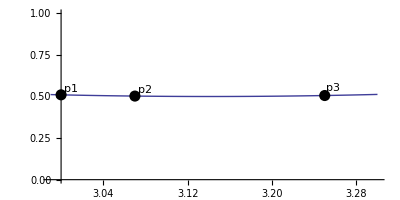

```mathematica
Plot[f[x],{x,2.99,3.3},Epilog->{PointSize[0.02], Point[{x1,f1}],Point[{x2,f2}],
Point[{x3,f3}],
Text["p1",Offset[{10,6},{x1,f1}]],
Text["p2",Offset[{10,6},{x2,f2}]],
Text["p3",Offset[{8,8},{x3,f3}]]
},PlotRange->{{2.99,3.3},{0,1}},AspectRatio->1/2,Ticks->{Automatic,{}}]
```

#### An example where a change of sign is detected

The next example shows a case where f[x] has the same sign at x1, x2, and x3 and a secant step gives a new approximation inside of Interval[{x2,x3}].  When f[x] is sampled at the new estimate we find that it has opposite sign than it did at x1 and x2.  If f[x] is continuous over Interval[{x2, x3}] there are two roots in the interval, and Brent's method can normally converge on them easily.  So in a case such as this my GoldenSecant method refines the approximation using Brent's method with starting values {x2,  newX} and {newX, x3}.

```mathematica
f[x_]:=Cos[x-0.2]-0.1;

{x1,x2,x3}={0.4,1.1,6.0};
{f1,f2,f3}={f[x1],f[x2],f[x3]}
```

{0.880067,0.52161,0.78552}

```mathematica
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1]);
{newX,f[newX]}
```

{2.11861,-0.440842}

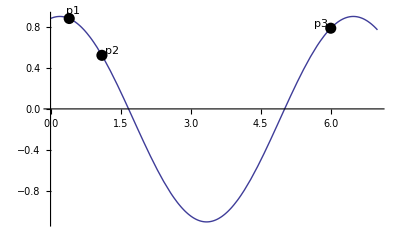

```mathematica
Plot[f[x],{x,0,7},Epilog->{PointSize[0.02], Point[{x1,f1}],Point[{x2,f2}],Point[{x3,f3}],
Text["p1",Offset[{4,8},{x1,f1}]],
Text["p2",Offset[{10,4},{x2,f2}]],
Text["p3",Offset[{-10,4},{x3,f3}]]
}]
```

#### An example where we need to prevent slow convergence

Consider using the secant method on the following function with starting values 
(x1, x2, x3) = {-2.23, 11.9, 12.0}.  Several steps of secant iteration on this example are shown below.  In this case the secant method hops back and forth gradually closing in on a root.

```mathematica
f[x_]:=If[x<7,(9-x)^0.8,x^0.73-1/(x-7)];
{x1,x2,x3}={-2.41,-2.4,11.9};
{f1,f2,f3}={f[x1],f[x2],f[x3]}
```

{7.01178,7.00687,5.89338}

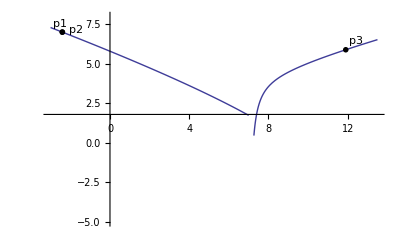

```mathematica
Block[{$DisplayFunction=Identity},
plt1=Plot[f[x],{x,-3,6.999999999}];
plt2=Plot[f[x],{x,7.000000001,13.5}];
txt=Graphics[{PointSize[0.01], Point[{x1,f1}],Point[{x2,f2}],Point[{x3,f3}],
Text["p1",Offset[{-2,8},{x1,f1}]],
Text["p2",Offset[{14,2},{x2,f2}]],
Text["p3",Offset[{10,9},{x3,f3}]]}];
];
Show[plt1,plt2,txt,PlotRange->{{-3,13.5},{-5,8}}]
```

```mathematica
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

11.8512

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

-2.25586

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

11.8319

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

-2.226

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

11.8102

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

-2.20786

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

11.8042

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

-2.19557

```mathematica
{x1,x2,x3}={x3,newX,x2};
newX=x2-f[x2]*(x2-x1)/(f[x2]-f[x1])
```

11.8004

To prevent slow convergence such as this my GoldenSecant algorithm checks to see if the secant step is changing direction.  When the secant step does change direction a Golden-Section find minimum step is taken if the secant step would have been larger than a Golden-Section step which is approximately  0.381966*Abs[x3-x2].

### References

Over several years I read everything I could find on algorithms for finding roots in one dimension.  Only a few of these references directly influenced the RootSearch algorithm and references to them can be found above.  Nearly everything I have learned on the subject is covered in one of the following.

G. E. Alefeld, F.A. Potra, Yixun Shi 1995, Algorithm 748: Enclosing Zeros of Continuous Functions, ACM Transactions on Mathematical Software, Vol 21, No 3, Sept 1995, 327-344.

G. E. Alefeld, F. A. Potra,Yixun Shi 1993, Mathematics of Computation, Vol 61, No 204, Oct 1993, 733-744.

G. E. Alefeld, F. A. Potra 1992, Some Simple Methods for Enclosing Simple Zeros of Nonlinear Equations, BIT 32 (1992), 334-344.

Ned Anderson, Åke Björck 1973, A New High Order Method of Regula Falsi Type for Computing a Root of an Equation, BIT 13, 1973, 253-264.

J. C. P. Bus, T. J. Dekker 1975, Two Efficient Algorithms With Guaranteed Convergence for Finding a Zero of a Function, ACM Transactions on Mathematical Software, Vol 1, No 4, Dec 1975, 330-345.

Kendal E. Atkinson 1989, An Introduction to Numerical Analysis, 2nd edition, (John Wiley & Sons).

R.P.Brent 1971, An Algorithm With Guaranteed Convergence for Finding a Zero of a Function, Computer Journal, vol 14 (1971), 422-425.

R.P.Brent 1973, Algorithms For Minimization Without Derivatives (Englewood Cliffs,NJ:Prentice-Hall).

Carl-Erik Fröberg 1985, Numerical Mathematics Theory and Computer Applications, (Benjamin Cummings Publishing).

R. F. King 1976, Methods without Secant Steps for Finding a Bracketed Root, Computing 17, 1976, 49-57.

F. M. Larkin 1980, Root-Finding by Fitting Rational Functions, Mathematica of Computation, Vol 35, No 151, July 1980, 803-816.

D. Le 1985, Three New Rapidly Convergent Algorithms for Finding a Zero of a Function, SIAM J. Stat Comput. 
Vol 6, No 1, Jan 1985, 193-208.

D. Le 1985, An Efficient Derivative-Free Method for Solving Nonlinear Equations, ACM Transactions on Mathematical Software, Vol 11, No 3, Sept 1985, 250-262.

Victor Norton 1985, ALGORITHM 631 Finding a Bracketed Zero by Larkin's Method of Rational Interpolation, ACM Transactions on Mathematical Software, Vol 11, No 2, June 1985, 120-134.

William H.Press, Saul A.Teukolsky, William T.Vetterling, Brian P.Flannery 1994, Numerical Recipes in C 
(Cambridge University Press).

Anthony Ralston, Phillip Rabinowitz, A First Course in Numerical Analysis 1978, McGraw-Hill Book Co.

C. J. F. Ridders 1979, Three-Point Iterations Derived From Exponential Curve Fitting, IEE Transactions on Circuits and Systems, Vol CAS-26, No 8, Aug 1979, 669-670.

G. W. Stewart 1993, On Infinitely Many Algorithms for Solving Equations, 
University of Maryland College Park TR-92-121, TR-2990.

J. F. Traub 1964, Iterative Methods for the Solution of Equations, Pretince-Hall Inc., Englewood Cliffs NJ.

Shröeder's Method from the MathWorld site at  http://mathworld.wolfram.com/SchroedersMethod.html

http://mathworld.wolfram.com/HalleysMethod.html

http://mathworld.wolfram.com/HouseholdersMethod.html